This notebook is to study the effect of N for kinetic+ rotation energy on length distribution.

```mathematica
A=2
J=4
gamma = 10
JkrN=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^Num l^3×(l-1)^2×ⅇ^(-u×l))-1,{u,-0.0001}],{Num,10000,30000,5000},{x,0.1,20,0.1}]
```

2

4

10

{{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.0021082,0.00196193,0.00182588,0.00169929,0.00158142,0.00147158,0.00136907,0.00127321,0.00118334,0.00109881,0.00101903,0.000943427,0.000871484,0.000802738,0.000736776,0.000673238,0.000611809,0.000552217,0.000494227,0.000437637,0.000382274,0.00032799,0.000274657,0.000222165,0.00017042,0.00011934,0.0000688554,0.000018904,-0.0000305672,-0.0000796045,-0.000128249,-0.000176535,-0.000224495,-0.000272157,-0.000319544,-0.000366679,-0.000413581,-0.000460267,-0.000506753,-0.000553053,-0.000599179,-0.000645142,-0.000690954,-0.000736622,-0.000782156,-0.000827564,-0.000872852,-0.000918026,-0.000963093,-0.00100806,-0.00105293,-0.0010977,-0.00114239,-0.001187,-0.00123152,-0.00127597,-0.00132035,-0.00136465,-0.00140889,-0.00145306,-0.00149717,-0.00154122,-0.00158522,-0.00162915,-0.00167303,-0.00171687,-0.00176065,-0.00180438,-0.00184806,-0.0018917,-0.00193529,-0.00197884,-0.00202235,-0.00206582,-0.00210925,-0.00215264,-0.002196,-0.00223931,-0.0022826,-0.00232584,-0.00236906,-0.00241224,-0.00245539,-0.00249851,-0.0025416,-0.00258466,-0.00262769,-0.00267069,-0.00271366,-0.00275661,-0.00279953,-0.00284242,-0.00288529,-0.00292814,-0.00297095,-0.00301375,-0.00305652,-0.00309927,-0.003142,-0.0031847,-0.00322739,-0.00327005,-0.00331269,-0.00335531,-0.00339791,-0.00344049},{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137061,0.00127591,0.00118777,0.00110572,0.00102928,0.000957991,0.000891398,0.00082906,0.000770543,0.000715432,0.000663336,0.000613893,0.000566773,0.000521681,0.000478355,0.000436566,0.000396117,0.000356835,0.000318571,0.000281199,0.000244609,0.000208707,0.000173413,0.000138657,0.000104379,0.0000705278,0.0000370578,3.9305×10^-6,-0.000028888,-0.0000614274,-0.0000937134,-0.000125769,-0.000157614,-0.000189266,-0.000220741,-0.000252053,-0.000283215,-0.000314236,-0.000345129,-0.0003759,-0.000406559,-0.000437113,-0.000467567,-0.00049793,-0.000528205,-0.000558397,-0.000588513,-0.000618554,-0.000648526,-0.000678432,-0.000708275,-0.000738059,-0.000767785,-0.000797457,-0.000827077,-0.000856647,-0.00088617,-0.000915647,-0.00094508,-0.00097447,-0.00100382,-0.00103313,-0.00106241,-0.00109164,-0.00112084,-0.00115001,-0.00117915,-0.00120825,-0.00123733,-0.00126637,-0.00129538,-0.00132437,-0.00135333,-0.00138226,-0.00141117,-0.00144006,-0.00146891,-0.00149775,-0.00152656,-0.00155535,-0.00158412,-0.00161287,-0.00164159,-0.0016703,-0.00169898,-0.00172765,-0.0017563,-0.00178493,-0.00181354,-0.00184214,-0.00187071,-0.00189927,-0.00192782,-0.00195634,-0.00198486,-0.00201335,-0.00204183,-0.0020703,-0.00209875,-0.00212719},{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137062,0.00127594,0.00118785,0.00110589,0.00102963,0.000958658,0.000892601,0.00083109,0.000773775,0.000720312,0.000670365,0.000623604,0.000579706,0.000538363,0.000499282,0.000462192,0.000426846,0.000393025,0.000360531,0.000329194,0.000298864,0.000269411,0.000240726,0.00021271,0.000185284,0.000158375,0.000131923,0.000105876,0.000080189,0.0000548223,0.0000297425,4.9204×10^-6,-0.0000196697,-0.00004405,-0.00006824,-0.0000922568,-0.000116116,-0.00013983,-0.000163411,-0.00018687,-0.000210216,-0.000233457,-0.000256601,-0.000279655,-0.000302624,-0.000325515,-0.000348332,-0.000371079,-0.000393761,-0.000416382,-0.000438944,-0.000461452,-0.000483908,-0.000506314,-0.000528674,-0.000550988,-0.000573261,-0.000595492,-0.000617685,-0.000639841,-0.000661961,-0.000684048,-0.000706101,-0.000728123,-0.000750115,-0.000772078,-0.000794013,-0.000815921,-0.000837802,-0.000859659,-0.000881491,-0.0009033,-0.000925086,-0.000946849,-0.000968592,-0.000990314,-0.00101202,-0.0010337,-0.00105536,-0.001077,-0.00109863,-0.00112024,-0.00114183,-0.00116341,-0.00118497,-0.00120651,-0.00122804,-0.00124955,-0.00127105,-0.00129253,-0.001314,-0.00133546,-0.0013569,-0.00137834,-0.00139975,-0.00142116,-0.00144255,-0.00146393,-0.0014853,-0.00150666},{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137063,0.00127594,0.00118785,0.00110589,0.00102963,0.000958679,0.000892653,0.000831208,0.000774018,0.000720779,0.000671199,0.000624998,0.000581903,0.000541647,0.000503965,0.0004686,0.000435305,0.000403845,0.000374002,0.000345577,0.000318392,0.000292287,0.000267123,0.000242779,0.000219149,0.000196144,0.000173684,0.000151702,0.000130142,0.000108954,0.0000880938,0.0000675261,0.0000472187,0.0000271441,7.27845×10^-6,-0.0000123992,-0.0000319069,-0.0000512605,-0.000070474,-0.0000895598,-0.000108529,-0.00012739,-0.000146153,-0.000164824,-0.000183411,-0.00020192,-0.000220356,-0.000238724,-0.000257029,-0.000275274,-0.000293463,-0.0003116,-0.000329688,-0.000347729,-0.000365726,-0.000383681,-0.000401596,-0.000419474,-0.000437316,-0.000455124,-0.0004729,-0.000490645,-0.000508359,-0.000526046,-0.000543705,-0.000561338,-0.000578946,-0.00059653,-0.00061409,-0.000631628,-0.000649145,-0.000666641,-0.000684116,-0.000701572,-0.00071901,-0.000736429,-0.000753831,-0.000771215,-0.000788583,-0.000805935,-0.000823272,-0.000840593,-0.0008579,-0.000875192,-0.00089247,-0.000909735,-0.000926987,-0.000944225,-0.000961452,-0.000978665,-0.000995868,-0.00101306,-0.00103024,-0.0010474,-0.00106456,-0.00108171,-0.00109884,-0.00111597,-0.00113309,-0.00115019},{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137063,0.00127594,0.00118785,0.00110589,0.00102963,0.00095868,0.000892655,0.000831213,0.000774033,0.000720815,0.00067128,0.000625167,0.000582227,0.000542225,0.00050493,0.000470119,0.00043757,0.000407067,0.0003784,0.000351367,0.00032578,0.000301464,0.000278261,0.000256029,0.000234645,0.000213999,0.000193995,0.000174552,0.000155599,0.000137075,0.000118929,0.000101114,0.0000835925,0.0000663312,0.0000493011,0.0000324776,0.0000158389,-6.33653×10^-7,-0.0000169564,-0.0000331436,-0.0000492078,-0.0000651599,-0.0000810097,-0.0000967658,-0.000112436,-0.000128026,-0.000143544,-0.000158993,-0.000174379,-0.000189706,-0.000204979,-0.0002202,-0.000235374,-0.000250502,-0.000265588,-0.000280633,-0.000295641,-0.000310614,-0.000325552,-0.000340458,-0.000355334,-0.00037018,-0.000384999,-0.000399791,-0.000414558,-0.000429301,-0.000444021,-0.000458719,-0.000473395,-0.000488051,-0.000502687,-0.000517304,-0.000531903,-0.000546484,-0.000561048,-0.000575596,-0.000590128,-0.000604645,-0.000619146,-0.000633634,-0.000648107,-0.000662567,-0.000677014,-0.000691448,-0.00070587,-0.00072028,-0.000734678,-0.000749064,-0.00076344,-0.000777804,-0.000792158,-0.000806502,-0.000820836,-0.00083516,-0.000849475,-0.00086378,-0.000878076,-0.000892364,-0.000906642,-0.000920912}}

```mathematica
Gamma1 = JkrN[[1]]
Gamma2 = JkrN[[2]]
Gamma3= JkrN[[3]]
Gamma4=JkrN[[4]]
Gamma5= JkrN[[5]]
```

{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.0021082,0.00196193,0.00182588,0.00169929,0.00158142,0.00147158,0.00136907,0.00127321,0.00118334,0.00109881,0.00101903,0.000943427,0.000871484,0.000802738,0.000736776,0.000673238,0.000611809,0.000552217,0.000494227,0.000437637,0.000382274,0.00032799,0.000274657,0.000222165,0.00017042,0.00011934,0.0000688554,0.000018904,-0.0000305672,-0.0000796045,-0.000128249,-0.000176535,-0.000224495,-0.000272157,-0.000319544,-0.000366679,-0.000413581,-0.000460267,-0.000506753,-0.000553053,-0.000599179,-0.000645142,-0.000690954,-0.000736622,-0.000782156,-0.000827564,-0.000872852,-0.000918026,-0.000963093,-0.00100806,-0.00105293,-0.0010977,-0.00114239,-0.001187,-0.00123152,-0.00127597,-0.00132035,-0.00136465,-0.00140889,-0.00145306,-0.00149717,-0.00154122,-0.00158522,-0.00162915,-0.00167303,-0.00171687,-0.00176065,-0.00180438,-0.00184806,-0.0018917,-0.00193529,-0.00197884,-0.00202235,-0.00206582,-0.00210925,-0.00215264,-0.002196,-0.00223931,-0.0022826,-0.00232584,-0.00236906,-0.00241224,-0.00245539,-0.00249851,-0.0025416,-0.00258466,-0.00262769,-0.00267069,-0.00271366,-0.00275661,-0.00279953,-0.00284242,-0.00288529,-0.00292814,-0.00297095,-0.00301375,-0.00305652,-0.00309927,-0.003142,-0.0031847,-0.00322739,-0.00327005,-0.00331269,-0.00335531,-0.00339791,-0.00344049}

{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137061,0.00127591,0.00118777,0.00110572,0.00102928,0.000957991,0.000891398,0.00082906,0.000770543,0.000715432,0.000663336,0.000613893,0.000566773,0.000521681,0.000478355,0.000436566,0.000396117,0.000356835,0.000318571,0.000281199,0.000244609,0.000208707,0.000173413,0.000138657,0.000104379,0.0000705278,0.0000370578,3.9305×10^-6,-0.000028888,-0.0000614274,-0.0000937134,-0.000125769,-0.000157614,-0.000189266,-0.000220741,-0.000252053,-0.000283215,-0.000314236,-0.000345129,-0.0003759,-0.000406559,-0.000437113,-0.000467567,-0.00049793,-0.000528205,-0.000558397,-0.000588513,-0.000618554,-0.000648526,-0.000678432,-0.000708275,-0.000738059,-0.000767785,-0.000797457,-0.000827077,-0.000856647,-0.00088617,-0.000915647,-0.00094508,-0.00097447,-0.00100382,-0.00103313,-0.00106241,-0.00109164,-0.00112084,-0.00115001,-0.00117915,-0.00120825,-0.00123733,-0.00126637,-0.00129538,-0.00132437,-0.00135333,-0.00138226,-0.00141117,-0.00144006,-0.00146891,-0.00149775,-0.00152656,-0.00155535,-0.00158412,-0.00161287,-0.00164159,-0.0016703,-0.00169898,-0.00172765,-0.0017563,-0.00178493,-0.00181354,-0.00184214,-0.00187071,-0.00189927,-0.00192782,-0.00195634,-0.00198486,-0.00201335,-0.00204183,-0.0020703,-0.00209875,-0.00212719}

{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137062,0.00127594,0.00118785,0.00110589,0.00102963,0.000958658,0.000892601,0.00083109,0.000773775,0.000720312,0.000670365,0.000623604,0.000579706,0.000538363,0.000499282,0.000462192,0.000426846,0.000393025,0.000360531,0.000329194,0.000298864,0.000269411,0.000240726,0.00021271,0.000185284,0.000158375,0.000131923,0.000105876,0.000080189,0.0000548223,0.0000297425,4.9204×10^-6,-0.0000196697,-0.00004405,-0.00006824,-0.0000922568,-0.000116116,-0.00013983,-0.000163411,-0.00018687,-0.000210216,-0.000233457,-0.000256601,-0.000279655,-0.000302624,-0.000325515,-0.000348332,-0.000371079,-0.000393761,-0.000416382,-0.000438944,-0.000461452,-0.000483908,-0.000506314,-0.000528674,-0.000550988,-0.000573261,-0.000595492,-0.000617685,-0.000639841,-0.000661961,-0.000684048,-0.000706101,-0.000728123,-0.000750115,-0.000772078,-0.000794013,-0.000815921,-0.000837802,-0.000859659,-0.000881491,-0.0009033,-0.000925086,-0.000946849,-0.000968592,-0.000990314,-0.00101202,-0.0010337,-0.00105536,-0.001077,-0.00109863,-0.00112024,-0.00114183,-0.00116341,-0.00118497,-0.00120651,-0.00122804,-0.00124955,-0.00127105,-0.00129253,-0.001314,-0.00133546,-0.0013569,-0.00137834,-0.00139975,-0.00142116,-0.00144255,-0.00146393,-0.0014853,-0.00150666}

{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137063,0.00127594,0.00118785,0.00110589,0.00102963,0.000958679,0.000892653,0.000831208,0.000774018,0.000720779,0.000671199,0.000624998,0.000581903,0.000541647,0.000503965,0.0004686,0.000435305,0.000403845,0.000374002,0.000345577,0.000318392,0.000292287,0.000267123,0.000242779,0.000219149,0.000196144,0.000173684,0.000151702,0.000130142,0.000108954,0.0000880938,0.0000675261,0.0000472187,0.0000271441,7.27845×10^-6,-0.0000123992,-0.0000319069,-0.0000512605,-0.000070474,-0.0000895598,-0.000108529,-0.00012739,-0.000146153,-0.000164824,-0.000183411,-0.00020192,-0.000220356,-0.000238724,-0.000257029,-0.000275274,-0.000293463,-0.0003116,-0.000329688,-0.000347729,-0.000365726,-0.000383681,-0.000401596,-0.000419474,-0.000437316,-0.000455124,-0.0004729,-0.000490645,-0.000508359,-0.000526046,-0.000543705,-0.000561338,-0.000578946,-0.00059653,-0.00061409,-0.000631628,-0.000649145,-0.000666641,-0.000684116,-0.000701572,-0.00071901,-0.000736429,-0.000753831,-0.000771215,-0.000788583,-0.000805935,-0.000823272,-0.000840593,-0.0008579,-0.000875192,-0.00089247,-0.000909735,-0.000926987,-0.000944225,-0.000961452,-0.000978665,-0.000995868,-0.00101306,-0.00103024,-0.0010474,-0.00106456,-0.00108171,-0.00109884,-0.00111597,-0.00113309,-0.00115019}

{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.00210821,0.00196197,0.00182596,0.00169948,0.00158184,0.00147241,0.00137063,0.00127594,0.00118785,0.00110589,0.00102963,0.00095868,0.000892655,0.000831213,0.000774033,0.000720815,0.00067128,0.000625167,0.000582227,0.000542225,0.00050493,0.000470119,0.00043757,0.000407067,0.0003784,0.000351367,0.00032578,0.000301464,0.000278261,0.000256029,0.000234645,0.000213999,0.000193995,0.000174552,0.000155599,0.000137075,0.000118929,0.000101114,0.0000835925,0.0000663312,0.0000493011,0.0000324776,0.0000158389,-6.33653×10^-7,-0.0000169564,-0.0000331436,-0.0000492078,-0.0000651599,-0.0000810097,-0.0000967658,-0.000112436,-0.000128026,-0.000143544,-0.000158993,-0.000174379,-0.000189706,-0.000204979,-0.0002202,-0.000235374,-0.000250502,-0.000265588,-0.000280633,-0.000295641,-0.000310614,-0.000325552,-0.000340458,-0.000355334,-0.00037018,-0.000384999,-0.000399791,-0.000414558,-0.000429301,-0.000444021,-0.000458719,-0.000473395,-0.000488051,-0.000502687,-0.000517304,-0.000531903,-0.000546484,-0.000561048,-0.000575596,-0.000590128,-0.000604645,-0.000619146,-0.000633634,-0.000648107,-0.000662567,-0.000677014,-0.000691448,-0.00070587,-0.00072028,-0.000734678,-0.000749064,-0.00076344,-0.000777804,-0.000792158,-0.000806502,-0.000820836,-0.00083516,-0.000849475,-0.00086378,-0.000878076,-0.000892364,-0.000906642,-0.000920912}

General::munfl: Exp[-711.121] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.377] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-725.633] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

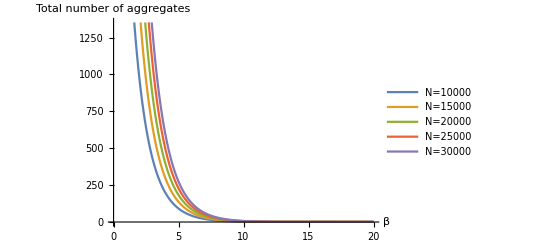

```mathematica
ListLinePlot[{(ⅇ^-Gamma1+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma1×l))/(ⅇ^-Gamma1+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma1×l))×10000,(ⅇ^-Gamma2+gamma×∑_(l=2)^15000 l^3×(l-1)^2×ⅇ^(-Gamma2×l))/(ⅇ^-Gamma2+gamma×∑_(l=2)^15000 l^4×(l-1)^2×ⅇ^(-Gamma2×l))×15000,(ⅇ^-Gamma3+gamma×∑_(l=2)^20000 l^3×(l-1)^2×ⅇ^(-Gamma3×l))/(ⅇ^-Gamma3+gamma×∑_(l=2)^20000 l^4×(l-1)^2×ⅇ^(-Gamma3×l))×20000,(ⅇ^-Gamma4+gamma×∑_(l=2)^25000 l^3×(l-1)^2×ⅇ^(-Gamma4×l))/(ⅇ^-Gamma4+gamma×∑_(l=2)^25000 l^4×(l-1)^2×ⅇ^(-Gamma4×l))×25000,(ⅇ^-Gamma5+gamma×∑_(l=2)^30000 l^3×(l-1)^2×ⅇ^(-Gamma5×l))/(ⅇ^-Gamma5+gamma×∑_(l=2)^30000 l^4×(l-1)^2×ⅇ^(-Gamma5×l))×30000},DataRange->{0,20},PlotLegends->{"N=10000","N=15000","N=20000","N=25000","N=30000"},AxesLabel->{"β","Total number of aggregates"}]
```

General::munfl: Exp[-711.121] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.377] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-725.633] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

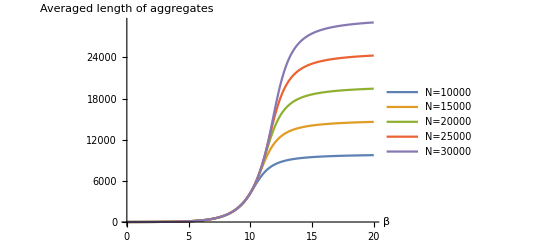

```mathematica
ListLinePlot[{(ⅇ^-Gamma1+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma1×l))/(ⅇ^-Gamma1+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma1×l)),(ⅇ^-Gamma2+gamma×∑_(l=2)^15000 l^4×(l-1)^2×ⅇ^(-Gamma2×l))/(ⅇ^-Gamma2+gamma×∑_(l=2)^15000 l^3×(l-1)^2×ⅇ^(-Gamma2×l)),(ⅇ^-Gamma3+gamma×∑_(l=2)^20000 l^4×(l-1)^2×ⅇ^(-Gamma3×l))/(ⅇ^-Gamma3+gamma×∑_(l=2)^20000 l^3×(l-1)^2×ⅇ^(-Gamma3×l)),(ⅇ^-Gamma4+gamma×∑_(l=2)^25000 l^4×(l-1)^2×ⅇ^(-Gamma4×l))/(ⅇ^-Gamma4+gamma×∑_(l=2)^25000 l^3×(l-1)^2×ⅇ^(-Gamma4×l)),(ⅇ^-Gamma5+gamma×∑_(l=2)^30000 l^4×(l-1)^2×ⅇ^(-Gamma5×l))/(ⅇ^-Gamma5+gamma×∑_(l=2)^30000 l^3×(l-1)^2×ⅇ^(-Gamma5×l))},DataRange->{0,20},PlotLegends->{"N=10000","N=15000","N=20000","N=25000","N=30000"},AxesLabel->{"β","Averaged length of aggregates"}]
```